```mathematica
ClearAll["Global`*"]
```

```mathematica
t2[r_, t_, i_, s_]:=(i-1)/(2s)t+(s-1)/(2i)r+r/(2i*s)*t;
t1[r_, t_, i_, s_]:=-2 √(r*t*(2i-r)*(2s-t));
EAM[r_, t_, i_, s_]:=t1[r, t, i, s]+t2[r, t, i ,s];
```

### Contour Plots for EAM

```mathematica
tmax=10;
rmax =10;
```

```mathematica
cp[f_]:=ContourPlot[f[r, t],{r,-rmax,rmax},{t,-tmax,tmax},PlotLegends->Automatic , Contours->14, FrameStyle->Directive[Black, Thick], FrameLabel->{"r","t"},LabelStyle->{18, Black, FontFamily->"Helvetica"} ,ClippingStyle->Automatic];
```

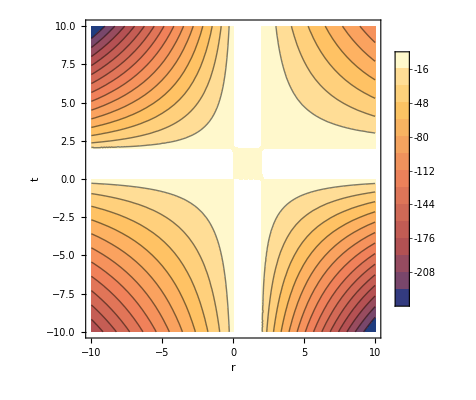

```mathematica
p0={1,1};
f0[r_,t_]:=EAM[r, t, Sequence@@p0];
cp[f0]
```

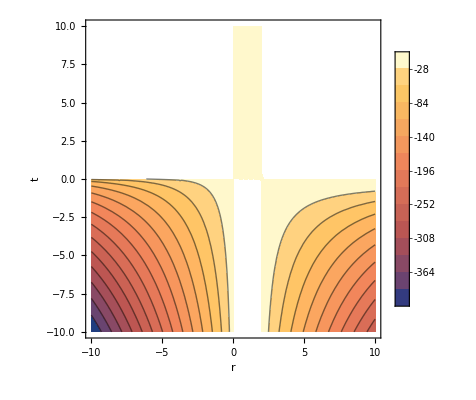

```mathematica
p1={1,10};
f1[r_,t_]:=EAM[r, t, Sequence@@p1];
cp[f1]
```

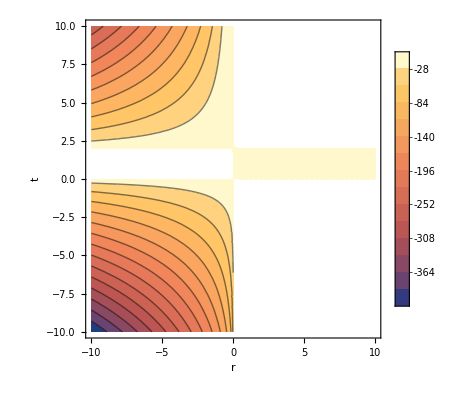

```mathematica
p2={10,1};
f2[r_,t_]:=EAM[r, t, Sequence@@p2];
cp[f2]
```

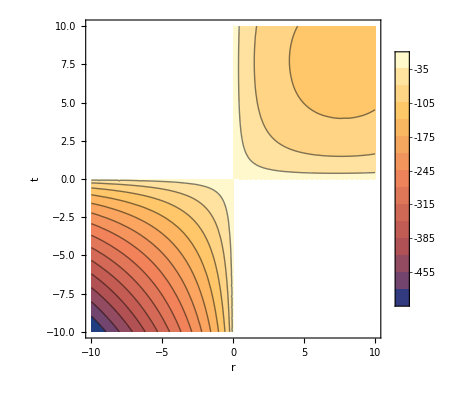

```mathematica
p3={8,8};
f3[r_,t_]:=EAM[r, t, Sequence@@p3];
cp[f3]
```

### Minima points for EAM